## Functions

```mathematica
UncertaintyPlus[{a_,σa_},X:{_,_}...]:=Fold[{#1[[1]]+#2[[1]],√((#1[[2]])^2+(#2[[2]])^2)}&,{a,σa},{X}]
UncertaintySubtract[{a_,σa_},{b_,σb_}]:={a-b,√(σa^2+σb^2)}
UncertaintyTimes[{a_,σa_},X:{_,_}...]:=Fold[{#1[[1]] #2[[1]],Abs[#1[[1]] #2[[1]]] √(((#1[[2]])/(#1[[1]]))^2+((#2[[2]])/(#2[[1]]))^2)}&,{a,σa},{X}]
UncertaintyDivide[{a_,σa_},{b_,σb_}]:={a/b,Abs[a/b] √((σa/a)^2+(σb/b)^2)}
```

### Importing

```mathematica
BuildFilePath[root_,date_,file_]:=root<>date<>"/"<>file<>"/"<>file<>".txt"
```

```mathematica
ImportDataFile[pathToFile_]:=Module[{nans,rawData},
nans=ConstantArray["nan",4];
rawData=Import[pathToFile,"Data"];
Developer`ToPackedArray/@Round/@Rest/@Most@Split[Prepend[rawData,nans],(#2=!=nans)&]
]
```

```mathematica
ImportDataFiles[pathToFiles_]:=Join@@(ImportDataFile/@pathToFiles)
```

```mathematica
ImportDataFiles[pathToFiles_]:=Module[{importedData},
importedData = ImportDataFile/@pathToFiles;
{Join@@(#),Length/@#}&@importedData]
```

```mathematica
CompensateDetectorLags[data_,lags_,lenStirap_]:=Module[{rules},

rules=Append[Rule@@@lags,_Integer:>0];

Function[{m},
With[{ls=m[[;;,1]]/.rules},
Transpose[{
m[[;;,1]],
Mod[m[[;;,2]]-ls,lenStirap],
m[[;;,3]]-ls,
m[[;;,4]]-UnitStep[ls-m[[;;,2]]]
}]
]
]/@data
]
```

### Filtering

```mathematica
(*Choosing to have crit@ rather than crit/@, crit must be Listable? Followup - indeed this seems to be the case, crit must be able to take a list (or is it list of lists...?)*)
FilterByCriteria[data_,columnSpec_, crit_,results_List]:=Pick[data,crit@data[[;;,;;,columnSpec]],#]&/@results
FilterByCriteria[data_,columnSpec_, crit_,result_]:=Pick[data,crit@data[[;;,;;,columnSpec]],result]

(*A slightly faster, Listable, implementation of a Between function, only valid for Integers and returns 1 for in range, 0 for below and 2 for above (Between returns True or False). *)
FastBetween[x_,{min_,max_}]:=UnitStep[x-min]+UnitStep[x-max-1]

FilterByDetector[data_,detectors_]:=FilterByCriteria[data,1,Identity,detectors]
FilterByPulseParities[data_,parities_List]:=FilterByCriteria[data,4,#,True]&/@parities
FilterByPulseParities[data_,parity_]:=FilterByCriteria[data,4,parity,True]
FilterByPulseRange[data_,{min_,max_}]:=FilterByCriteria[data,4,FastBetween[#,{min,max}]&,1]
FilterByStirapRange[data_,{min_,max_}]:=FilterByCriteria[data,2,FastBetween[#,{min,max}]&,1]
```

```mathematica
CorrelatedDetections[data_,det1_,det2_,i_Integer]:=Module[{allDetectionPairs},
First@CorrelatedDetections[data,det1,det2,{i}]
]

CorrelatedDetections[data_,det1_,det2_,idx_List]:=Module[{allDetectionPairs},
allDetectionPairs=If[det1==det2,
Flatten[Subsets[#,{2}]&/@FilterByDetector[data,det1],1],
Flatten[Outer[List,#[[1,;;]],#[[2,;;]],1]&/@Transpose[FilterByDetector[data,{det1,det2}]],2]
];

With[{detectionPulseNumberDiffs=allDetectionPairs[[;;,1,4]]-allDetectionPairs[[;;,2,4]]},
Pick[allDetectionPairs,detectionPulseNumberDiffs,#]&/@idx
]
]
```

```mathematica
(*FilterPairsByArrival[detectionPairs_,FirstOrLast_/;MemberQ[{First,Last},FirstOrLast]]:=FirstOrLast@Transpose[SortBy[#,#[[3]]&]&/@detectionPairs]*)
```

```mathematica
(*Options[FilterCorrelationPairs]={
"FirstOrLast"->(Flatten[#,1]&),
"Detector"->_,
"Parity"->(Map[True&,#]&)
};

FilterCorrelationPairs[correlationPairs_,OptionsPattern[]]:=
FilterByPulseParities[FilterByDetector[{OptionValue["FirstOrLast"][Transpose[SortBy[#,#[[3]]&]&/@correlationPairs]]},OptionValue["Detector"]],OptionValue["Parity"]]*)
```

```mathematica
Options[FilterCorrelationPairs]={
"FirstOrLast"->"Either",
"Detector"->"Either",
"Parity"->"Either"
};

FilterCorrelationPairs[correlationPairs_,OptionsPattern[]]:=Module[{correlationSingles},
correlationSingles=List@If[
OptionValue["FirstOrLast"]==="Either",
Flatten[correlationPairs,1],
OptionValue["FirstOrLast"][Transpose[SortBy[#,#[[3]]&]&/@correlationPairs]]
];

correlationSingles=If[
OptionValue["Detector"]==="Either",
correlationSingles,
FilterByDetector[correlationSingles,OptionValue["Detector"]]
];

correlationSingles=If[
OptionValue["Parity"]==="Either",
correlationSingles,
FilterByPulseParities[correlationSingles,OptionValue["Parity"]]
];

First@correlationSingles
]
```

### Statistics

```mathematica
HomCorrelations[data_,detPairs:{{_Integer,_Integer}..},func_:Subtract]:=Module[{assoc,emptyAssoc,flatRiffledData,ditheredDiffs,homBunches,groupbyInput},

flatRiffledData=Join@@Riffle[DeleteCases[data,{}],{{{-1,-1,-1,-1}}}];
ditheredDiffs=(Prepend[#,1]*Append[#,1])&@Differences[flatRiffledData[[;;,4]]];
homBunches=SplitBy[Pick[flatRiffledData,ditheredDiffs,0],Last];
groupbyInput=Transpose/@Flatten[Subsets[#,{2}]&/@homBunches,1];

assoc=GroupBy[groupbyInput,First->(#[[2]]&)];

emptyAssoc=AssociationThread[#->ConstantArray[{},Length[#]]]&@Union[detPairs,Reverse/@detPairs];
assoc=Merge[{assoc,emptyAssoc},Flatten[#,1]&];

Map[func@@#&,
If[SameQ@@#,assoc[#],Flatten[{assoc[#],Reverse/@assoc[Reverse@#]},1]]&/@detPairs,
{2}
]
]
```

```mathematica
Correlations[data_,det1_,det2_,column_]:=
If[det1==det2,
(#[[;;,2]]-#[[;;,1]])&@(Join@@(Subsets[#[[;;,column]],{2}]&/@FilterByDetector[data,det1])),
Flatten[
Outer[Plus,#[[1,;;,column]],-#[[2,;;,column]]]&/@Transpose[FilterByDetector[data,{det1,det2}]]
]
]
```

```mathematica
RealPhotonsPerThrow[data_,atomWindow_,backWindow_]:=Module[{nAtom,nBack,σAtom,σBack,scaleFactor},

nAtom=Length[Flatten[FilterByPulseRange[data,atomWindow],1]];
nBack=Length[Flatten[FilterByPulseRange[data,backWindow],1]];

scaleFactor=(Subtract@@atomWindow)/(Subtract@@backWindow);

σAtom=√nAtom;
σBack=√nBack;

{nAtom,σAtom}={nAtom,σAtom}/Length[data];
{nBack,σBack}=scaleFactor{nBack,σBack}/Length[data];

N@{{nAtom-nBack,√(σAtom^2+σBack^2)},{nBack,σBack}}

]
```

```mathematica
NCorrelationsPerThrow[data_,detectors_List,idx_List,idxBack_List:Range[101,200]]:=Module[{correls,countsDet1,countsDet2,backCorrels},

{correls,backCorrels}=Transpose[
Table[
Total/@{#[[idx]],#[[idxBack]]}&@SparseArray[Rule@@@Tally[Select[Correlations[data,i,j,4],Positive]],{25000}],{i,detectors},{j,detectors}],
{2,3,1}
];

backCorrels=backCorrels/(Length[idxBack]/Length[idx]);

N@Transpose[{correls-backCorrels,√(correls+backCorrels)}/Length[data],{3,1,2}]
]
```

```mathematica
TotalCorrelationsPerThrow[data_,det1_,det2_]:=UncertaintyPlus@@Flatten[NCorrelationsPerThrow[data,{det1,det2},Range[100]],1]

PM1CorrelationsPerThrow[data_,det1_,det2_]:=UncertaintyPlus@@Flatten[NCorrelationsPerThrow[data,{det1,det2},{1}],1]
```

### Plotting

```mathematica
LabelledMOTHistogram[data_,atomLims_,notAtomLims_]:=Module[{binWidth,nNotAtoms,backLevel,nBins=50},

nNotAtoms=Count[Flatten[data[[;;,;;,4]]],x_/;Between[x,notAtomLims]];
backLevel= nNotAtoms/(nBins((#[[2]]-#[[1]]&)@notAtomLims)/motPlotMax);
backLevel=backLevel/(Length[data](motPlotMax photonLength 10^-12/10^-3)/nBins);

Histogram[Flatten[data[[;;,;;,4]]],{0,motPlotMax,motPlotMax/nBins},Function[{bins,counts},counts/(Length[data](motPlotMax photonLength 10^-12/10^-3)/nBins)],
FrameTicks->{Automatic,{Automatic,Transpose[{#,photonLength#/1.*^9}]&@Range[0,motPlotMax,motPlotMax/5]}},
Epilog->{
Dashed,Line[{{0,backLevel},{motPlotMax,backLevel}}],Opacity[0.2],
Green,Rectangle[Scaled[{atomLims[[1]]/motPlotMax,0}],Scaled[{atomLims[[2]]/motPlotMax,1}]],Red,Rectangle[Scaled[{notAtomLims[[1]]/motPlotMax,0}],Scaled[{notAtomLims[[2]]/motPlotMax,1}]]
},
FrameLabel->{{"Counts per Throw per ms",None},{"Pulse Number","MOT time / ms"}},
AspectRatio->1/2,
genOpts
]
]
```

```mathematica
LabelledG2Histogram[data_,det1_,det2_]:=Module[{correls11,correls12,correls22,bc11,bc12,bc22,lspData11,lspData12,lspData22,EpiLabelF},

correls11=Developer`ToPackedArray@Correlations[data,det1,det1,4];
correls12=Developer`ToPackedArray@Correlations[data,det1,det2,4];
correls22=Developer`ToPackedArray@Correlations[data,det2,det2,4];

bc11=BinCounts[-correls11,{-binLimit,1}];
bc12=BinCounts[correls12,{-binLimit,binLimit+1}];
bc22=BinCounts[correls22,{0,binLimit+1}];
{bc11,bc12,bc22}/=Length[data];

{lspData11,lspData12,lspData22}=
{
Riffle[#[[1;;;;2]],0],
Riffle[#[[2;;;;2]],0,{1,-1,2}]
}&/@{bc11,bc12,bc22};

EpiLabelF[{d1_,d2_},{x_,y_}]:=Text[StringForm["Det `1` - Det `2`",d1, d2],Scaled[{x,y}],Scaled[Round[{x,y},0.05]],Background->Directive[Opacity[0.8],White]];

With[{opts=Sequence[
PlotRange->{All,{0,5Ceiling[Max[{bc11,bc12,bc22}]/5.,0.001]}},
PlotStyle->None,
Filling->{1->{Axis,Directive[Opacity[0.7],ColorData[97][4]]},2->{Axis,Directive[Opacity[0.7],ColorData[97][1]]}},
FrameTicks->{Automatic,{Automatic,Transpose[{#,photonLength#/1.*^6}]&@FindDivisions[{-binLimit,binLimit},5]}},
genOpts
]},
Row@{
ListStepPlot[lspData11,"Center",DataRange->{-binLimit,0},AspectRatio->1,Epilog->{EpiLabelF[{det1,det1},{0.02,0.98}]},
FrameLabel->{{"Correlatoins per MOT throw",None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},opts],
ListStepPlot[lspData12,"Center",DataRange->{-binLimit,binLimit},AspectRatio->1/2,Epilog->{EpiLabelF[{det1,det2},{0.02,0.98}]},
FrameLabel->{{None,None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},opts],
ListStepPlot[lspData22,"Center",DataRange->{0,binLimit},AspectRatio->1,Epilog->{EpiLabelF[{det2,det2},{0.98,0.98}]},
FrameLabel->{{None,None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},opts]
}
]
]
```

```mathematica
LabelledG2HistogramTriangle[data_,detectors_]:=Module[{IdxT,correls,bc,lsp,EpiLabelF},

IdxT[{i_,j_}]:={i,i+j-1};

correls=Table[Developer`ToPackedArray@Correlations[data,detectors[[i]],detectors[[j]],4],{i,1,Length[detectors]},{j,i,Length[detectors]}];

bc=MapIndexed[
If[Equal@@IdxT[#2],
BinCounts[-#1,{-binLimit,1}],
BinCounts[#1,{-binLimit,binLimit+1}]
]/Length[data]&,correls,{2}];

lsp=Map[{Riffle[#[[1;;;;2]],0],Riffle[#[[2;;;;2]],0,{1,-1,2}]}&,bc,{2}];

EpiLabelF[{d1_,d2_},{x_,y_}]:=Text[StringForm["Det `1` - Det `2`",d1, d2],Scaled[{x,y}],Scaled[Round[{x,y},0.05]],Background->Directive[Opacity[0.8],White]];

With[{opts=Sequence[
PlotRange->{All,{0,5Ceiling[Max[bc]/5.,0.001]}},
PlotStyle->None,
Filling->{1->{Axis,Directive[Opacity[0.7],ColorData[97][4]]},2->{Axis,Directive[Opacity[0.7],ColorData[97][1]]}},
FrameTicks->{Automatic,{Automatic,Transpose[{#,photonLength#/1.*^6}]&@FindDivisions[{-binLimit,binLimit},5]}},
genOpts
]},
Grid[PadLeft[#,Length[detectors],Null]&/@MapIndexed[
ListStepPlot[#1,"Center",DataRange->If[Equal@@IdxT[#2],{-binLimit,0},{-binLimit,binLimit}],AspectRatio->1,Epilog->{EpiLabelF[{detectors[[IdxT[#2][[1]]]],detectors[[IdxT[#2][[2]]]]},{0.02,0.98}]},
FrameLabel->{{"Correlatoins per MOT throw",None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},opts]&,
lsp,
{2}
]
]
]
]
```

```mathematica
StirapSubHistogram[data_,atomWindow_,backWindow_,nbins_,col_,opts:OptionsPattern[]]:=Module[{dataAtom,dataBack,nAtom,nBack,σAtom,σBack,N1,N2,bc,backLvl,amp,limitedPhotonLength},

limitedPhotonLength=-Subtract@@stirapLimits;

dataAtom=Flatten[FilterByPulseRange[data,atomWindow][[;;,;;,2]]];
dataBack=Flatten[FilterByPulseRange[data,backWindow][[;;,;;,2]]];

nAtom=Length[dataAtom];
nBack=Length[dataBack];

σAtom=√nAtom;
σBack=√nBack;

N1=N@Length[data];
N2=limitedPhotonLength/nbins 10^-6;

{nAtom,σAtom}={nAtom,σAtom}/N1;
{nBack,σBack}=(Subtract@@atomWindow)/(Subtract@@backWindow){nBack,σBack}/N1;

bc=BinCounts[dataAtom,{0.,limitedPhotonLength,limitedPhotonLength/nbins}]/(N1 N2);

backLvl=(nBack/nbins)/N2;
amp=(Max[bc]-backLvl);

ListStepPlot[bc,"Center",DataRange->{0.,limitedPhotonLength/1000.},
PlotStyle->Directive[AbsoluteThickness[0.8],Black],
Filling->{1->{Axis,col}},
Epilog->{
{Opacity[0.5],Black,Rectangle[{0,0},{limitedPhotonLength/1000,backLvl}]},
{First@Plot[{
backLvl+amp Sin[π x/(limitedPhotonLength/1000)]^2,
backLvl+amp Sin[π x/(limitedPhotonLength/1000)]^4
},{x,0,limitedPhotonLength/1000},PlotStyle->{Directive[Black,Opacity[0.5],Dotted],Directive[Black,Opacity[0.5],Dashed]}]},
{Text[StringRiffle[UncertaintyForm[#,1]&/@{{nAtom-nBack,√(σAtom^2+σBack^2)},{nBack,σBack}},"\n"],Scaled[{0.98,0.98}],Scaled[{1,1}],Background->Directive[Opacity[1],White]]}
},
opts
]
]
```

```mathematica
TotalGrid[g_,f_:Total]:=ArrayFlatten[{{g,{Map[f,g]}ᵀ},{{Map[f,gᵀ]},{{f@Flatten[g,1]}}}},2]
```

```mathematica
DetectionGrid[data_,detectors_]:=Module[{subdividedData,subdividedDataGrid,nbins,max,hopts,cols,frameLabels},

subdividedData=FilterByDetector[#,detectors]&/@FilterByPulseParities[data,{EvenQ,OddQ}];
subdividedDataGrid=TotalGrid[subdividedData,Map[Join@@#&,Transpose@#]&];

nbins=25;
max=Max[HistogramList[Flatten[#[[;;,;;,2]]],{0,photonLength,photonLength/20}][[2]]&/@Join[subdividedDataGrid[[;;2,3]],subdividedDataGrid[[3,;;2]]]];
hopts=Sequence[Frame->True,GridLines->Automatic,PlotRangePadding->None,PlotRange->{{0,photonLength/1000.},{0,5Ceiling[max/5.]/($NTHROWS photonLength/nbins 10^-6)}},ImageSize->200,AspectRatio->0.8];

cols=Map[ColorData[97],{{4,Sequence@@ConstantArray[1,Length[detectors]-1],3},{4,Sequence@@ConstantArray[1,Length[detectors]-1],3},{2,Sequence@@ConstantArray[2,Length[detectors]-1],5}},{2}];

frameLabels={{
{{"Evens",None},{None,"Detector "<>ToString[detectors[[1]]]}},
Sequence@@({{"",None},{None,"Detector "<>ToString[#]}}&/@detectors[[2;;]]),
{{"",None},{None,"All Detectors"}}
},{
{{"Odds",None},{None,""}},
Sequence@@ConstantArray[{{"",None},{None,""}},{6}]
},{
{{"Both Parities",None},{None,""}},
Sequence@@ConstantArray[{{"",None},{None,""}},{6}]
}};

Grid@MapIndexed[
StirapSubHistogram[#1,atomWindow,backWindow,nbins,cols[[Sequence@@#2]],FrameLabel->frameLabels[[Sequence@@#2]],hopts]&,
subdividedDataGrid,
{2}
]
]
```

### Formatting

```mathematica
UncertaintyForm[{a_,b_},p_:2]:=NumberForm[
SetAccuracy[a±b,Accuracy@SetPrecision[b,p]],
NumberFormat->(If[#3=!="",StringJoin[{#1,Table["0",Abs@ToExpression@#3-1]}],#1]&),
ExponentFunction->(Null&)
]//ToString//Quiet
```

```mathematica
PadDecimalStrings[string_,{l1_,lt_}]:=StringRiffle[
StringPadRight[StringRepeat[" ",l1-With[{sp=StringPosition["0","."]},If[sp==={},StringLength["0"],sp[[1,1]]]]]<>#,lt]&/@StringSplit[string][[{1,-1}]],
"±"]
```

### Derived Statistics

```mathematica
AtomsPerThrowPM1[Np_,Nc1_,T_]:=(Np^2(T-1))/(Nc1 T^2)
PhotonEfficiencyPM1[Np_,Nc1_,T_]:=(Nc1 T)/(Np (T-1))
```

```mathematica
AtomsPerThrowPM1[{Np_,σNp_},{Nc1_,σNc1_},T_]:={(Np^2(T-1))/(Nc1 T^2),(T-1)/T^2 Np^2/Nc1 √(((2Np σNp)/Np^2)^2+(σNc1/Nc1)^2)}
PhotonEfficiencyPM1[{Np_,σNp_},{Nc1_,σNc1_},T_]:={(Nc1 T)/(Np (T-1)),T/(T-1)Nc1/Np √((σNc1/Nc1)^2+(σNp/Np)^2)}
```

```mathematica
AtomsPerThrow[Np_,NcAll_,T_]:=(Np^2(T-1))/(2 NcAll T)
PhotonEfficiency[Np_,NcAll_,T_]:=(2 NcAll)/(Np (T-1))
```

```mathematica
AtomsPerThrow[{Np_,σNp_},{NcAll_,σNcAll_},T_]:={(Np^2(T-1))/(2 NcAll T),(T-1)/(2 T)Np^2/NcAll √(((2Np σNp)/Np^2)^2+(σNcAll/NcAll)^2)}
PhotonEfficiency[{Np_,σNp_},{NcAll_,σNcAll_},T_]:={(2 NcAll)/(Np (T-1)),2/(T-1)NcAll/Np √((σNcAll/NcAll)^2+(σNp/Np)^2)}
```

Tom : I think this is the correct version  - don' t understand why Oli factored the interaction time, T, into these equations.

```mathematica
PhotonEfficiency[{Np_,σNp_},{NcAll_,σNcAll_}]:={(2 NcAll)/Np,2 NcAll/Np √((σNcAll/NcAll)^2+(σNp/Np)^2)}
```

### Wilson score

```mathematica
CorrectedWilsonScore[n_,x_,α_]:=With[{p=x/n,z=Sqrt[2] InverseErf[α]},{Max[0,(2 n p+z^2-(z Abs@Sqrt[z^2-1/n+4 n p (1-p)+(4 p-2)]+1))/(2 (n+z^2))],Min[1,(2 n p+z^2+(z Abs@Sqrt[z^2-1/n+4 n p (1-p)-(4 p-2)]+1))/(2 (n+z^2))]}]
```

### γ-factor calculation

```mathematica
NumberHomBackgroundCorrelations[data_,{detA_,detB_},dataLimits_]:=Module[{dataA,dataB,bins},
{dataA,dataB}=Flatten[#[[;;,;;,4]]]&/@FilterByDetector[data,{detA,detB}];
bins=Append[dataLimits,1];
N[ListConvolve[BinCounts[dataA,bins],Reverse[BinCounts[dataB,bins]]][[1]]/Length[data]]
]


CorrelationEnvelope[data_,{detA_,detB_},dataLimits_,nBins_: 101]:=Module[{dataA,dataB,binWidth,bins},{dataA,dataB}=Flatten[#[[;;,;;,2]]]&/@FilterByDetector[data,{detA,detB}];
binWidth=-Subtract@@dataLimits/nBins;
bins=dataLimits[[1]]+binWidth Range[-1,nBins+1];
Interpolation[
Transpose[{
ListConvolve[#,Reverse[#],{1,-1},-∞,Subtract,Min]&@MovingAverage[bins,2],
1/(Length[dataA] Length[dataB] binWidth) ListConvolve[BinCounts[dataA,{bins}],Reverse[BinCounts[dataB,{bins}]],{1,-1},0]
}][[2;;-2]],
InterpolationOrder->1
]
]
```

## Usage New

ToDo:
	Handle when attempting to import files which aren’t there or have no data
	Make it so that the only files listed as available to import are folder with actual data txt files in (as the folder grets created at the start of a run and the txt file at the end. (or not, Tom lines them up early)
	Including when also selected empty folders...

### Import New

```mathematica
folderForm=__~~"-"~~__~~"-"~~__;
```

```mathematica
root="/Volumes/KuhnGroup/Results017_New/data/";
```

```mathematica
root="Z:\\Results017_New\\data\\";
```

```mathematica
Panel[
Column[{
Labeled[
InputField[Dynamic[root],String],
"Root",Top],
Labeled[
PopupMenu[Dynamic[date],Reverse@(FileNameTake/@FileNames[folderForm,root])],
"Date",Left],
Labeled[Row[{
Dynamic@ListPicker[Dynamic[files],Reverse@(FileNameTake/@FileNames[folderForm,root<>date])],
Column[{
Button["Update",odate=date;date="00-00-00";date=odate;,ImageSize->{80,80}],
Button["Copy File Names",CopyToClipboard[StringRiffle[files,", "]]]
}]
}],
"Files",Left],
Button["Import",
{data1Raw,dataFileLengths}=ImportDataFiles[BuildFilePath[root,date,#]&/@Reverse[files]];,
Method->"Queued"
],

Dynamic["Length data = "<>ToString[Length[data1Raw]]]
}]
]
```

Root
Date
Update
Copy File NamesFiles
Import

```mathematica
files={"20-14-17","19-28-13","18-42-00","17-56-02","17-32-38","17-09-10","16-45-17","15-26-51","15-03-22"};
```

### Display

#### Analysis definition

```mathematica
genOpts=Sequence[PlotRange->All,Frame->True,GridLines->Automatic,PlotRangePadding->None,ImageSize->{Automatic,320}];
```

```mathematica
ANALYSIS[data1Raw_]:=Module[{},
data2Limited=Select[data1Raw,Between[Length[#],coarseCountCutOffs]&];
data2Limited=CompensateDetectorLags[data2Limited,Transpose[{Sort[detectors],lag[#]&/@Sort[detectors]}],photonLength];
data2Limited=FilterByStirapRange[data2Limited,stirapLimits];
data2Limited=Select[data2Limited,Between[Length[#],fineCountCutOffs]&];

$NTHROWS=Length[data2Limited];

p1=LabelledMOTHistogram[data2Limited,atomWindow,backWindow];

{Np,σNp}=RealPhotonsPerThrow[data2Limited,atomWindow,backWindow][[1]];

data3Windowed=FilterByPulseRange[data2Limited,atomWindow];

p2=ListLinePlot[Length/@data3Windowed,FrameLabel->{{"Counts",None},{"Throw Number",""}},PlotRange->{0,All},FrameTicks->{Automatic,{Automatic,All}},AspectRatio->1/2,genOpts];

g3=DetectionGrid[data2Limited,detectors];

p6=If[Length[detectors]==2,
LabelledG2Histogram[data3Windowed,detectors[[1]],detectors[[2]]],
LabelledG2HistogramTriangle[data3Windowed,detectors]
];

{NcAll,σNcAll}=TotalCorrelationsPerThrow[data3Windowed,detectors[[1]],detectors[[2]]];
{Nc1,σNc1}=PM1CorrelationsPerThrow[data3Windowed,detectors[[1]],detectors[[2]]];

pads={5,12};

infoTable=TableForm[{
{"Interaction Time:", ToString[tInter]<>"  ⟺  "<>ToString[tInter photonLength/10.^6]<>" μs"},
{"",""},
{"Number MOT Throws:", Length[data2Limited]},
{"",""},
{"Real photons per throw:", PadDecimalStrings[UncertaintyForm[{Np,σNp}],pads]},
{"All Correlations per throw:",  PadDecimalStrings[UncertaintyForm[{NcAll,σNcAll}],pads]},
{"±1 Correlations per throw:", PadDecimalStrings[UncertaintyForm[{Nc1,σNc1}],pads]},
{"",""},
{"Atoms per throw:",PadDecimalStrings[UncertaintyForm@AtomsPerThrow[{Np,σNp},{NcAll,σNcAll},tInter],pads]},
{"Photon efficiency:",PadDecimalStrings[UncertaintyForm@PhotonEfficiency[{Np,σNp},{NcAll,σNcAll},tInter],pads]}
{"",""}
(*{"Atoms per throw (±1):",PadDecimalStrings[UncertaintyForm@AtomsPerThrowPM1[{Np,σNp},{Nc1,σNc1},tInter],pads]},
{"Photon efficiency (±1):",PadDecimalStrings[UncertaintyForm@PhotonEfficiencyPM1[{Np,σNp},{Nc1,σNc1},tInter],pads]}*)
}];

Grid[{
{p1,p2,If[Length[detectors]>2,infoTable,SpanFromLeft]},
{p6,SpanFromLeft},
{g3,If[Length[detectors]==2,infoTable,SpanFromLeft],SpanFromLeft}
}]
]
```

#### Run

664000

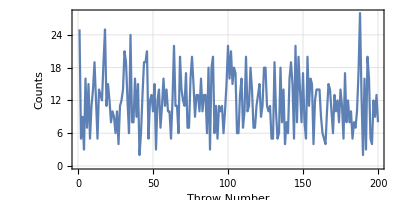
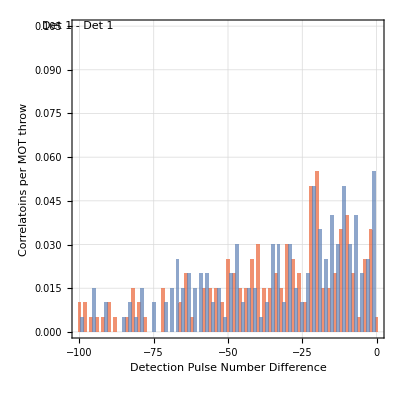
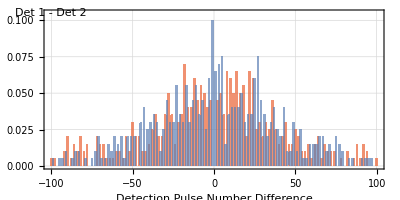
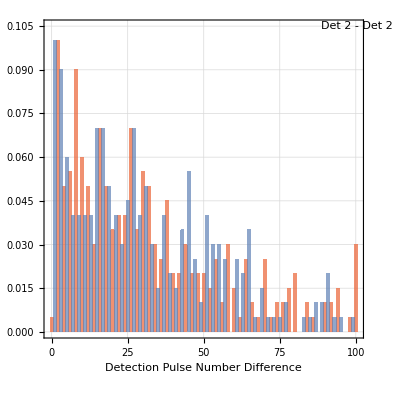
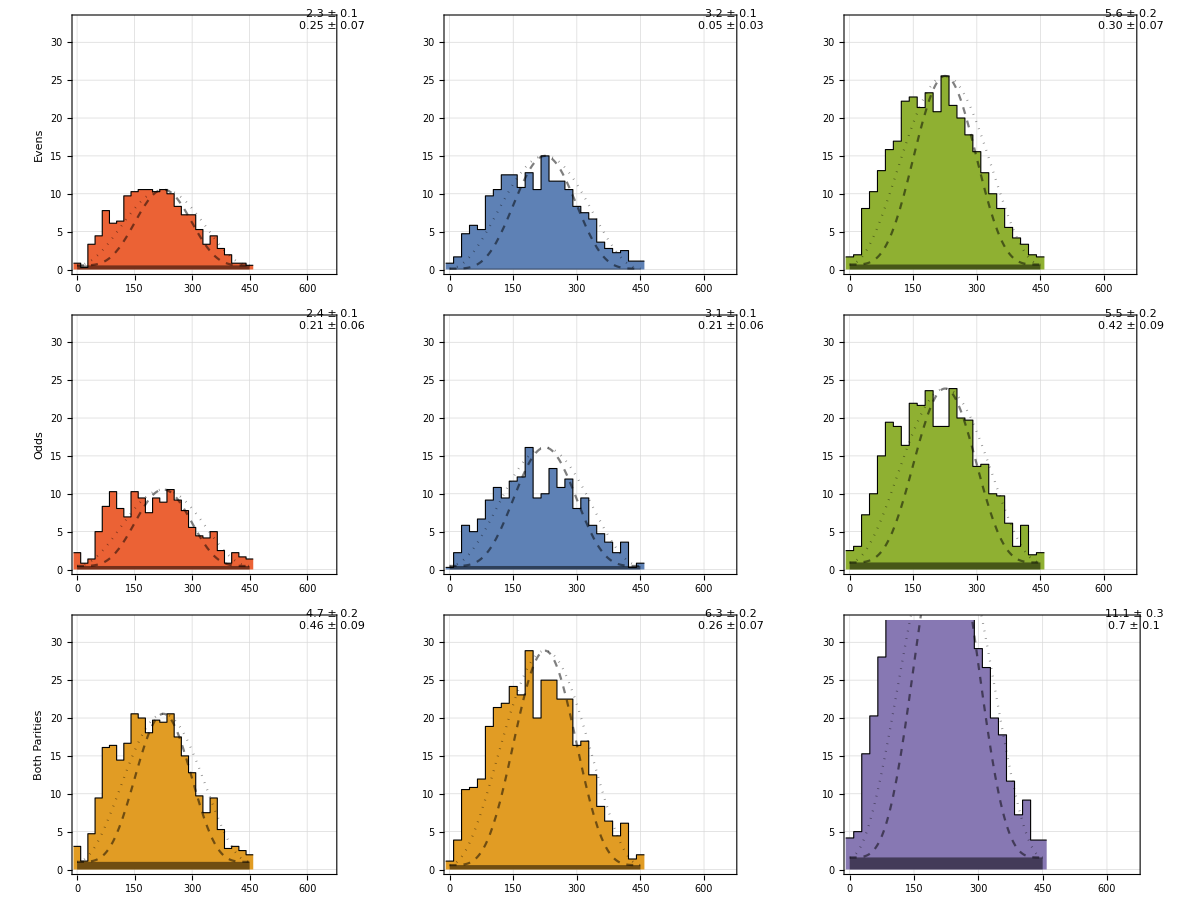
-Graphics- | -Graphics- | 
-Graphics--Graphics--Graphics- |  | 
-Graphics- | Interaction Time: | 30  ⟺  19.92 μs
 | 
Number MOT Throws: | 200
 | 
Real photons per throw: |     11.05   ±    0.27    
All Correlations per throw: |     7.19    ±    0.24    
±1 Correlations per throw: |     0.301   ±    0.041   
 | 
Atoms per throw: |     8.22    ±    0.48    
 Photon efficiency: |      0.0448  ±    0.0018   |

```mathematica
coarseCountCutOffs={0,500};
fineCountCutOffs={0,50};

atomWindow=Round[{0,14}10^3];
backWindow=Round[{16,20}10^3];
motPlotMax=10000*2;
detectors={1,2};

photonLength =664*10^3
lag[0]=lag[1]=lag[2]=lag[3]=lag[4]=lag[5]=lag[6]=lag[7]=lag[8]=160*10^3;
lag[1]+=photonLength;

stirapLimits={0,450}10^3  ;

tInter=30;

binLimit=100;(*Chose an even number*)

ANALYSIS[data1Raw]
```

#### Photon generation efficiency for randomly routed photons

Total number of photon detections.

```mathematica
{Np,σNp}=RealPhotonsPerThrow[data2Limited,atomWindow,backWindow][[1]]
```

{11.0525,0.267219}

Total number of +/-1 correlations by detector pairings.

```mathematica
{Nc12, σNc12}=PM1CorrelationsPerThrow[data3Windowed,detectors[[1]],detectors[[2]]]
{Nc11, σNc11} = PM1CorrelationsPerThrow[data3Windowed,detectors[[1]],detectors[[1]]]
{Nc22, σNc22} =PM1CorrelationsPerThrow[data3Windowed,detectors[[2]],detectors[[2]]]
{NcSame,σNcSame}=UncertaintyPlus[{Nc11, σNc11},{Nc22, σNc22} ]
{NcAll,σNcAll}=UncertaintyPlus[UncertaintyPlus[{Nc11, σNc11},{Nc22, σNc22} ],{Nc12, σNc12}]
```

{0.30065,0.0411916}

{0.2086,0.0340147}

{0.3722,0.0462493}

{0.5808,0.0574108}

{0.88145,0.0706594}

Calculate the end-to-end efficiency (i.e. given at atom coupled to the cavity, what is the chance of a photon detection).

```mathematica
PhotonEfficiencyTB[{Np_,σNp_},{NcAll_,σNcAll_}]:=UncertaintyDivide[{NcAll,σNcAll},{Np,σNp}]
ηMeas = PhotonEfficiencyTB[{Np,σNp},{NcAll,σNcAll}]
```

{0.0797512,0.00667751}

Check the theoretical limit.  This is a combination of:
	ηgen: photon generation efficiency in the cavity
	ηext: extraction efficiency from the cavity (i.e. out-coupler transmission compared to total losses)
	ηloss: average loss through from coupling and transmission from cavity to detectors
	ηdet: average detector efficiency
	ηrep: repumping efficiency
	
Note: We can find the total losses in the cavity by knowing the out-coupling mirror transmission is ~40ppm and the cavity finesse is ~117,000.

```mathematica
T1 = 0*10^-6;
T2 = 40*10^-6;
L1 = L2= 6.8*10^-6;
R1 = 1 - T1 - L1;
R2 = 1 - T2 - L2;
R  = √(R1*R2);

F[R_] := (3.14 * √R)/(1-R);
ηext=T2/(T1+T2+L1+L2)
F[R]
```

0.746269

117162.

Make some reasonable guesses for the best-case-scenario of the other efficiencies.

```mathematica
{ηgen,ηloss,ηdet,ηrep}={0.7,0.65,0.85,0.95};
ηMax= ηgen*ηext*ηloss*ηdet*ηrep
```

0.274188

Therefore we can see that we are this fraction of the best possible performance:

```mathematica
ηMeas[[1]]/ηMax
```

0.290863

#### Histogram of individual transits and burst counts

```mathematica
byThrows=Association[#->GroupBy[data3Windowed[[#]],#[[4]]&]&/@Range[Length@data3Windowed]];
```

```mathematica
Keys[byThrows[1]]
```

{1745,2005,2698,4676,4683,4915,4918,4945,5077,5260,5651,6215,6527,7303,7455,7520,7535,8073,8575,8934,8955,8980,11910,11925,12822}

```mathematica
Manipulate[Module[{byThrow},
Histogram[Keys@byThrows[iThrow],{0,20000,binWidth}]
],
{iThrow,1,Length@data3Windowed,1},
{binWidth,1,100,1}]
```

{{0,397811},{1,2046},{2,126},{3,14},{4,3}}

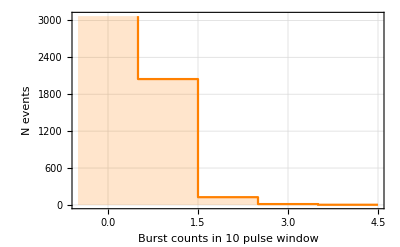

```mathematica
binWidth=10;
byThrowsHists=HistogramList[Keys@#,{0,20000,binWidth}]&/@byThrows;
(*byThrowsHistsPlottable={MovingAverage[#[[1]],2],#[[2]]}ᵀ&/@byThrowsHists;*)

burstCounts=Flatten[Values[Tally[#[[2]]]&/@byThrowsHists],1];
burstValues=Union[burstCounts[[;;,1]]];
bursts={#,Total[Select[burstCounts,Function[bc,bc[[1]]==#]][[;;,2]]]}&/@burstValues
ListStepPlot[bursts, 
"Center",
PlotRange->{All,{0,1.5*Max[bursts[[2;;]]]}},
PlotStyle->Orange,
Filling->Axis, 
PlotRangePadding->0,
FrameLabel->{{"N events",None},{"Burst counts in "<>ToString[binWidth]<>" pulse window",None}},
genOpts
]
```

### MMI

#### Functions

```mathematica
CountRatesByDetector[data_]:=Module[{filteredData, atomData, backData, nAtom,σAtom,nBack,σBack, limitedPhotonLength, N1, N2},

filteredData=FilterByDetector[data,detectors];
atomData = Flatten[FilterByPulseRange[#,atomWindow][[;;,;;,2]]]&/@filteredData;
backData= Flatten[FilterByPulseRange[#,backWindow][[;;,;;,2]]]&/@filteredData;

{nAtom,nBack} = Length/@#&/@{atomData,backData};
{σAtom,σBack} = √{nAtom,nBack};

limitedPhotonLength=-Subtract@@stirapLimits;
N1=N@Length[data2Limited];
N2=limitedPhotonLength/nbins 10^-6;
{nAtom,σAtom}={nAtom,σAtom}/N1;
{nBack,σBack}=(Subtract@@atomWindow)/(Subtract@@backWindow){nBack,σBack}/N1;

Transpose/@{{nAtom-nBack,√(σAtom^2+σBack^2)},{nBack,σBack}} 
]

CountCorrelations[data_,detPairs_,detectionDiff_]:=Module[{corrs, countedCorrs},
corrs = Correlations[data,#[[1]],#[[2]],4]&/@detectorPairs;
countedCorrs = Function[correlsList,Sort@Abs@Tally[correlsList,Abs[#1]==Abs[#2]&]]/@corrs;
Select[#,#[[1]]==detectionDiff&][[1,2]]&/@countedCorrs
]

Matrix3D[m_,lab_]:=Module[{box},
box[h_,{x_,y_}]:={ColorData["Rainbow",h/Max[m]],Cuboid[{x,y,0},{x+1,y+1,10*h}]};
Labeled[
Graphics3D[
MapIndexed[box,Transpose@m,{2}],
Boxed->False,
ImageSize->300
],
lab,
Bottom
]
]
```

#### MMI

```mathematica
(*dataTarget = data3Windowed;*)
dataTarget=FilterByPulseParities[data3Windowed,OddQ];

{n44, n55,n66,n77,n45,n46,n47,n56,n57,n67}=Length/@HomCorrelations[dataTarget,{{4,4},{5,5},{6,6},{7,7},{4,5},{4,6},{4,7},{5,6},{5,7},{6,7}}];

(*γ44=γ55=γ66=γ77=1.8;*)

mMMI=({{n44*γ44, n45, n46, n47}, {0, n55*γ55, n56, n57}, {0, 0, n66*γ66, n67}, {0, 0, 0, n77*γ77}})
Total@{n44, n55,n66,n77,n45,n46,n47,n56,n57,n67}
```

{{3.57903,19,8,35},{0,85.2939,93,35},{0,0,16.1911,10},{0,0,0,47.9045}}

285

```mathematica
Matrix3D[1/(Total@Flatten@mMMI)mMMI,"mMMI"]
```

-Graphics3D-mMMI

MMI γ-factor calculations

```mathematica
dix=Outer[List,detectors,detectors]
correls=Map[First[HomCorrelations[data3Windowed,{#}]]&,dix,{2}];
ns=Map[Length,correls,{2}];
backs=Map[NumberHomBackgroundCorrelations[data3Windowed,#,atomWindow]&,dix,{2}];
minCorrels=Min[Abs[#]]&/@Diagonal[correls]
fs=CorrelationEnvelope[data3Windowed,#,stirapLimits]&/@Diagonal[dix];
γs=2.NIntegrate[#[[1]][t],{t,#[[2]],-Subtract@@stirapLimits}]&/@Transpose[{fs,minCorrels}]
```

{{{4,4},{4,5},{4,6},{4,7}},{{5,4},{5,5},{5,6},{5,7}},{{6,4},{6,5},{6,6},{6,7}},{{7,4},{7,5},{7,6},{7,7}}}

{59583,59502,58935,58612}

{0.558811,0.551036,0.555861,0.563621}

```mathematica
{γ44,γ55,γ66,γ77}=1/γs
```

{1.78951,1.81476,1.79901,1.77424}

Extract orthogonal data by splitting ratios (note - technically the 00 correlated counts should be excluded but they are such a small part of the sample).

```mathematica
{nCounts,nBacks}=CountRatesByDetector[FilterByPulseParities[data2Limited,OddQ]]
ζ=#/(Total@#)&@nCounts[[;;,1]];
```

{{{0.220711,0.00250122},{0.827025,0.004736},{0.332318,0.00301918},{0.48745,0.00371221}},{{0.00389039,0.000544764},{0.0047295,0.000600647},{0.00289872,0.000470235},{0.00823848,0.000792748}}}

Extract orthogonal data by correlations of photons in different time bases

```mathematica
detectorPairs={{4,4},{5,5},{6,6},{7,7},{4,5},{4,6},{4,7},{5,6},{5,7},{6,7}};
{n44o, n55o,n66o,n77o,n45o,n46o,n47o,n56o,n57o,n67o}=CountCorrelations[dataTarget, detectorPairs,2]
```

{7,127,28,43,85,30,36,102,168,64}

### Additional Analyses

#### Conditional Efficiencies - Tom

```mathematica
RealPhotons[data_,atomWindow_,backWindow_]:=Module[{nAtom,nBack,σAtom,σBack,scaleFactor},

nAtom=Length[Flatten[FilterByPulseRange[data,atomWindow],1]];
nBack=Length[Flatten[FilterByPulseRange[data,backWindow],1]];

scaleFactor=(Subtract@@atomWindow)/(Subtract@@backWindow);

σAtom=√nAtom;
σBack=√nBack;

{nAtom,σAtom}={nAtom,σAtom};
{nBack,σBack}=scaleFactor{nBack,σBack};

N@{{nAtom-nBack,√(σAtom^2+σBack^2)},{nBack,σBack}}

]
```

```mathematica
filteredData=fD=(FilterByPulseParities[#,{EvenQ,OddQ}]&/@FilterByDetector[data2Limited,{1,2}]);
d1Even=RealPhotons[fD[[1,1]],atomWindow,backWindow][[1]];
d1Odd=RealPhotons[fD[[1,2]],atomWindow,backWindow][[1]];
d2Even=RealPhotons[fD[[2,1]],atomWindow,backWindow][[1]];
d2Odd=RealPhotons[fD[[2,2]],atomWindow,backWindow][[1]];

nDenom={{d1Even,d2Even},{d1Odd,d2Odd}};

tabOpts=Sequence[TableHeadings->{{"Even","Odd"},("Det "<>ToString[#])&/@detectors}];

tDenom=TableForm[Map[UncertaintyForm,nDenom,{2}],tabOpts];

corr2cond1=CorrelatedDetections[data3Windowed,1,2,-1][[;;,2]];
corr1cond2=CorrelatedDetections[data3Windowed,2,1,-1][[;;,2]];
{corr2cond1Even,corr2cond1Odd}=Length[#[[1]]]&/@FilterByPulseParities[{corr2cond1},{EvenQ,OddQ}];
{corr1cond2Even,corr1cond2Odd}=Length[#[[1]]]&/@FilterByPulseParities[{corr1cond2},{EvenQ,OddQ}];

nNum=Map[{#,√#}&,
{{corr1cond2Even,corr2cond1Even},{corr1cond2Odd,corr2cond1Odd}},{2}];

tNum=TableForm[Map[UncertaintyForm,nNum,{2}],tabOpts];

nDenomConditioning=Reverse@Transpose@Reverse[Transpose@nDenom];
pCond=
Map[UncertaintyDivide@@#&,Transpose/@Transpose@{nNum,nDenomConditioning},{2}];
tCond=TableForm[Map[UncertaintyForm,pCond,{2}],tabOpts];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
Grid[{{
"Number of detections following a detection on the opposite detector in the previous interval",
tNum
},
{
"Number of detections on the given detector/parity pair",
tDenom
},
{"Conditional probabilities of detection given a detection on the opposite detector in the previous interval",
tCond
}}
]
```

Number of detections following a detection on the opposite detector in the previous interval |  | Det 1 | Det 2
Even | 0 ± 0 | 21.0 ± 4.58
Odd | 118.0 ± 10.86 | 1.0 ± 1.0
Number of detections on the given detector/parity pair |  | Det 1 | Det 2
Even | 757. ± 40. | 4079. ± 74.
Odd | 3216. ± 65. | 371. ± 42.
Conditional probabilities of detection given a detection on the opposite detector in the previous interval |  | Det 1 | Det 2
Even | 0 ± Indeterminate | 0.0065 ± 0.0014
Odd | 0.0289 ± 0.0027 | 0.0013 ± 0.0013

```mathematica
{p1cond2,p2cond1}={pCond[[2,1]],pCond[[1,2]]};
UncertaintyForm@UncertaintyDivide[p1cond2,p2cond1]
```

4.4 ± 1.1

#### Conditional Efficiencies

```mathematica
nNum=(Length/@Flatten[FilterByPulseParities[{CorrelatedDetections[data3Windowed,#[[1]],#[[2]],1][[;;,1]]},{EvenQ,OddQ}],1])&/@Transpose[{detectors,Reverse[detectors]}];
nDenom=Map[Length@Flatten[#,1]&,(FilterByDetector[#,Reverse@detectors]&/@FilterByPulseParities[data2Limited,{OddQ,EvenQ}]),{2}];

tabOpts=Sequence[TableHeadings->{{"Even","Odd"},("Det "<>ToString[#])&/@detectors}];

Grid[{{
"Number of detections following a detection on the opposite detector in the previous interval",
TableForm[nNum,tabOpts]
},
{
"Number of detections on the given detector",
TableForm[nDenom,tabOpts]
},
{
"Conditional Probabilities",
TableForm[Map[UncertaintyForm[UncertaintyDivide@@#]&,Transpose[{Transpose[{nNum,√nNum},{3,1,2}],Transpose[{nDenom,√nDenom},{3,1,2}]},{3,1,2}],{2}],tabOpts]
}},
ItemSize->25,
Spacings->{0,2},
Alignment->Top
]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Number of detections following a detection on the opposite detector in the previous interval |  | Det 1 | Det 2
Even | 0 | 118
Odd | 21 | 1
Number of detections on the given detector |  | Det 1 | Det 2
Even | 912 | 3588
Odd | 4619 | 1107
Conditional Probabilities |  | Det 1 | Det 2
Even | 0 ± Indeterminate | 0.0329 ± 0.003
Odd | 0.0045 ± 0.001 | 0.0009 ± 0.0009

```mathematica
{p2Con1,p1Cond2}=N/@{nNum[[1,2]]/nDenom[[2,1]],nNum[[2,1]]/nDenom[[1,2]]}
p2Con1/p1Cond2
```

{0.0255467,0.00585284}

4.36483

#### n̄ and HOM

```mathematica
{det1,det2} = detectors;
```

Calculate γ-factors for detectors.

```mathematica
dix=Outer[List,detectors,detectors]
dataTarget=FilterByPulseParities[data3Windowed,OddQ];
correls=Map[First[HomCorrelations[dataTarget,{#}]]&,dix,{2}];
ns=Map[Length,correls,{2}];
backs=Map[NumberHomBackgroundCorrelations[dataTarget,#,atomWindow]&,dix,{2}];
minCorrels=Min[Abs[#]]&/@Diagonal[correls]
fs=CorrelationEnvelope[dataTarget,#,stirapLimits]&/@Diagonal[dix];
γs=2.NIntegrate[#[[1]][t],{t,#[[2]],-Subtract@@stirapLimits}]&/@Transpose[{fs,minCorrels}]
```

{{{1,1},{1,2}},{{2,1},{2,2}}}

{59179,57883}

{0.50118,0.471566}

InterpolatingFunction::dmval: Input value {-599975.} lies outside the range of data in the interpolating function. Extrapolation will be used.

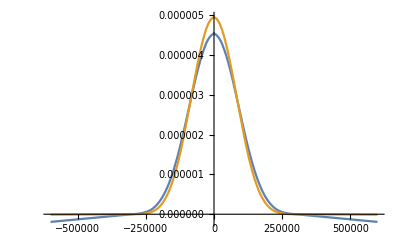

```mathematica
Plot[{fs[[1]][x],fs[[2]][x]},{x,-600000,600000}]
```

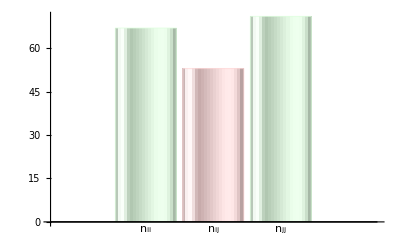

{0.157155,0.0215869}

{n̄, Δn̄} = {0.157155, 0.0215869}

{n_ij,n_ii+n_ij+n_jj} = {53, 191}

Visibility (with calcualted γs) = 68.569%

```mathematica
(*dataTarget = data3Windowed;*)
dataTarget=FilterByPulseParities[data3Windowed,OddQ];
(*dataTarget=lowVisDataLimited;*)

correlsHom=HomCorrelations[dataTarget,{{det1,det2} }][[1]];
{correlsHom00, correlsHom11}=HomCorrelations[dataTarget,{{det1,det1},{det2,det2}}];
{nii,nij,njj}=Length/@{correlsHom00,correlsHom,correlsHom11};
BarChart[{nii,nij,njj},ChartLabels->{"n_ii","n_ij","n_jj"},ChartStyle->{LightGreen, LightRed, LightGreen},ChartElementFunction->"GlassRectangle"]

(*Print["{n̄, Δn̄} = "<>ToString[N/@{nij/(nii+njj+nij),nij/(nii+njj+nij)√((√nij)/nij+(√nii+√nij+√njj)/(nii+njj+nij))}]]*)
(*{nbar, nbarErr} = N/@{nij/(nii+njj+nij),(√nij)/(nii+njj+nij)}
Print["{n̄, Δn̄} = "<>ToString[{nbar, nbarErr}]]
Print["{n_ij,n_ii+n_ij+n_jj} = "<>ToString[{nij,nii+njj+nij}]]
Print["Visibility (assuming (n̄)_perp=0.58) = "<>ToString[100*(1-nbar/0.58)]<>"%"]*)

{nbar, nbarErr} = N/@{nij/(1/γs[[1]] nii+1/γs[[2]] njj+nij),(√nij)/(1/γs[[1]] nii+1/γs[[2]] njj+nij)}
Print["{n̄, Δn̄} = "<>ToString[{nbar, nbarErr}]]
Print["{n_ij,n_ii+n_ij+n_jj} = "<>ToString[{nij,nii+njj+nij}]]
Print["Visibility (with calcualted γs) = "<>ToString[100*(1-2*nbar)]<>"%"]
```

```mathematica
1/γs[[1]] nii+1/γs[[2]] njj+nij
```

130.91

```mathematica
(nij-4)/(1/γs[[1]] nii+1/γs[[2]] njj+nij)
```

0.248475

```mathematica
correlsPara=correlsHom
```

{-39263,-119328,-10201,-128961,-141834,-116333,-109614,-221089,-192997,-128557,126776,65736,85488,220765,114470,17648,212750,70188,120057,166687,12305,60150,134953,35458}

```mathematica
correlsParaDouble=correlsHom;
```

{-380742,407133}

{88.9333 ns,22.4888 MHz}

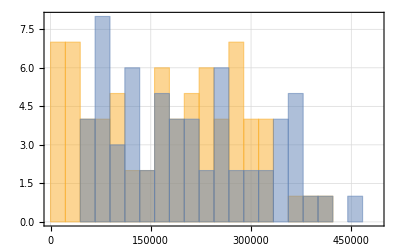

```mathematica
nbins=15;
MinMax@correlsHom
{#,UnitConvert[1/(0.5#),"MHz"]}&@Quantity[N@2photonLength*10^-3/nbins,"ns"]
(*homHist = Histogram[{correlsHom,Join[-1*correlsHom00,correlsHom11]},{-1.5*photonLength,1.5*photonLength,photonLength/nbins}/2,genOpts]*)
homHist = Histogram[{Abs@correlsHom,Abs@Join[-1*correlsHom00,correlsHom11]},{0,1.5*photonLength,photonLength/nbins}/2,genOpts]
```

```mathematica
3.24/14*13
```

3.00857

```mathematica
3
```

Plot the bin heights as a function of time.

```mathematica
data=data1Raw;

{throwWindowStart,throwWindowEnd, throwWindowWidth, thowWindowStep} =Round[{1,Length@data,1000,100}];
throwWindows = Table[{If[x==0,1,x],If[x+throwWindowWidth>Length@data,Length@data,x+throwWindowWidth]}, {x, throwWindowStart, throwWindowEnd-(throwWindowWidth-thowWindowStep), thowWindowStep}];

correlsHoms=FilterAndHomCorrelations[data1Raw[[ #[[1]];;#[[2]] ]],{{det1,det1},{det1,det2},{det2,det2}}]&/@throwWindows;
homHistLists = HistogramList[#,{-photonLength,photonLength,2photonLength/nbins}/2]&/@correlsHoms[[;;,2]];
homHistLists={0.5*(#[[1]][[;;-2]]+#[[1]][[2;;]]),#[[2]]}&/@homHistLists;
```

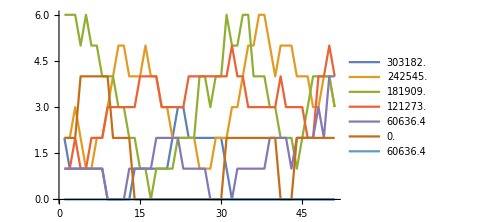

```mathematica
plotData =Module[{sortedHomHisLists},
sortedHomHisLists=Transpose[Transpose/@homHistLists];
Table[
{#[[1,1]],#[[;;,2]]}&@sortedHomHisLists[[i]],
{i,1,Length@sortedHomHisLists}
]
];

foldedPlotData=
Join[
Table[
{#[[-i,1]],#[[i,2]]+#[[-i,2]]}&@plotData,
{i,1,Round[Length@plotData/2,2]}
],
{plotData[[Round[Length@plotData/2,2]+1]]}
];

ListLinePlot[
foldedPlotData[[;;,2]],
PlotLegends-> foldedPlotData[[;;,1]],
ImageSize->Medium
]
```

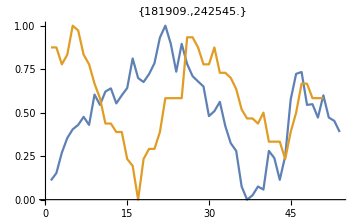
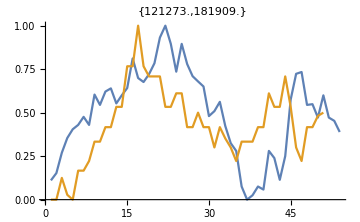
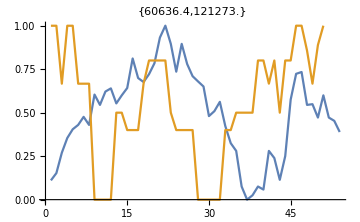

```mathematica
i={3,2};
plt1=ListLinePlot[
{
Rescale@nbars[[;;,1]],
Rescale[foldedPlotData[[;;,2]][[i[[1]]]]/(0.001+foldedPlotData[[;;,2]][[i[[1]]]]+foldedPlotData[[;;,2]][[i[[2]]]])]
},
PlotLabel->  foldedPlotData[[;;,1]][[i]],
ImageSize->Medium
];

i={4,3};
plt2=ListLinePlot[
{
Rescale@nbars[[;;,1]],
Rescale[foldedPlotData[[;;,2]][[i[[1]]]]/(0.001+foldedPlotData[[;;,2]][[i[[1]]]]+foldedPlotData[[;;,2]][[i[[2]]]])]
},
PlotLabel->  foldedPlotData[[;;,1]][[i]],
ImageSize->Medium
];

i={5,4};
plt3=ListLinePlot[
{
Rescale@nbars[[;;,1]],
Rescale[foldedPlotData[[;;,2]][[i[[1]]]]/(0.001+foldedPlotData[[;;,2]][[i[[1]]]]+foldedPlotData[[;;,2]][[i[[2]]]])]
},
PlotLabel->  foldedPlotData[[;;,1]][[i]],
ImageSize->Medium
];

Row[{plt1,plt2,plt3}]
```

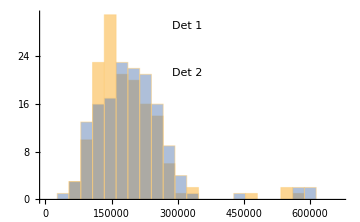
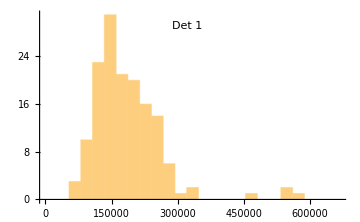
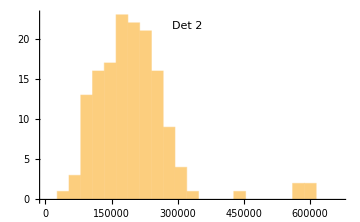

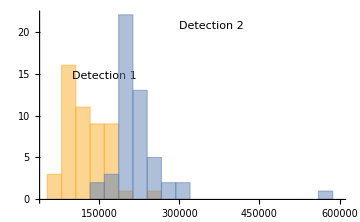
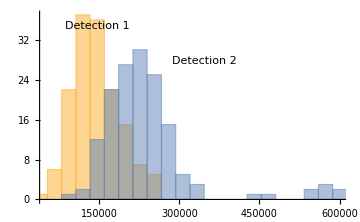
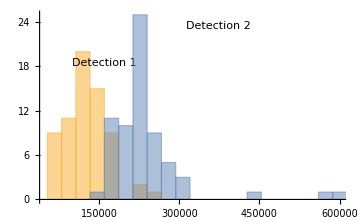

```mathematica
nBins = 25;
Row[{
Histogram[Transpose@Flatten[HomCorrelations[#,{{det1,det2}},List],1],{0,photonLength,photonLength/nBins}, ChartLabels->{"Det 1","Det 2"},ImageSize->Medium]&/@{ dataTarget},
Histogram[(Transpose@Flatten[HomCorrelations[#,{{det1,det2}},List],1])[[1]],{0,photonLength,photonLength/nBins},ChartLabels->{"Det 1"},ImageSize->Medium]&/@{ dataTarget},
Histogram[(Transpose@Flatten[HomCorrelations[#,{{det1,det2}},List],1])[[2]],{0,photonLength,photonLength/nBins}, ChartLabels->{"Det 2"},ImageSize->Medium]&/@{ dataTarget}
}]
Histogram[#,{0,photonLength,photonLength/nBins},ImageSize->Medium,PlotRange->{stirapLimits,Automatic}, ChartLabels->{"Detection 1","Detection 2"}]&/@Transpose/@(Map[Sort,#]&/@HomCorrelations[#,{{det1,det1},{det1,det2},{det2,det2}},List]&/@{dataTarget})[[1]]
```

```mathematica
det1SKD=SmoothKernelDistribution[(Transpose@Flatten[HomCorrelations[dataTarget,{{det1,det2}},List],1])[[1]]];
det2SKD=SmoothKernelDistribution[(Transpose@Flatten[HomCorrelations[dataTarget,{{det1,det2}},List],1])[[2]]];
homSKD=SmoothKernelDistribution[correlsHom,5000];
```

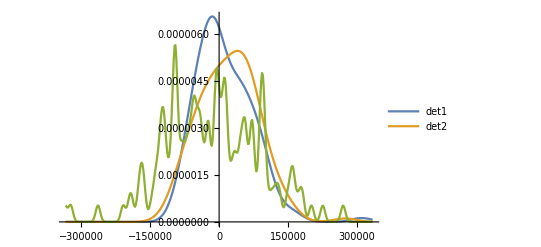

```mathematica
plt2=Plot[
{PDF[det1SKD,x+photonLength/4],PDF[det2SKD,x+photonLength/4],PDF[homSKD,x]},
{x,-photonLength/2,photonLength/2},
PlotLegends->{"det1", "det2"}]
```

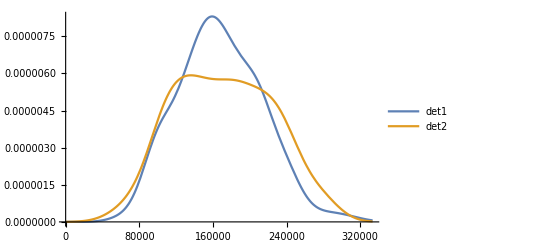
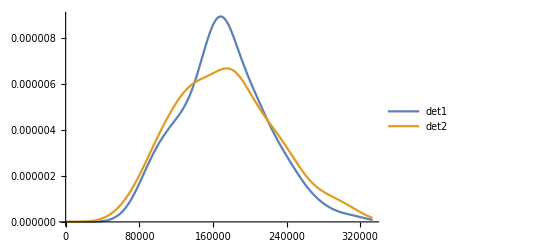

```mathematica
{plt1,plt2}
```

#### n̄ and HOM as function of MOT time

```mathematica
{det1,det2}=detectors;
```

```mathematica
HomCorrelationsWindowed[data_, detPairs_, atomWindow_]:=Module[{data3Windowed},
data3Windowed=FilterByPulseRange[data,atomWindow];
HomCorrelations[data3Windowed,detPairs]
]
HomBackgroundCorrelations[data_,{detA_,detB_}]:=N[ListConvolve[#1,Reverse@#2][[1]]/Length[data]]&@@(HistogramList[Flatten[#[[;;,;;,4]]],Append[MinMax[Flatten[data[[;;,;;,4]]]],1]][[2]]&/@FilterByDetector[data,{detA,detB}])
CorrectedHOMCorrelations[data_,detPairs:{{_Integer,_Integer}..}]:=(Length/@HomCorrelations[data,detPairs])-(If[#[[1]]==#[[2]],0.58,1] HomBackgroundCorrelations[data,#]&/@detPairs)
HomCorrelationsWindowedBkgCorr[data_, detPairs_, atomWindow_]:=Module[{data3Windowed},
data3Windowed=FilterByPulseRange[data,atomWindow];
CorrectedHOMCorrelations[data3Windowed,detPairs]
]
```

```mathematica
Needs["ErrorBarPlots`"]
MakeNice[x_,y_,σy_]:=Sort@Transpose[{Transpose[{x,y}],ErrorBar/@σy}]
```

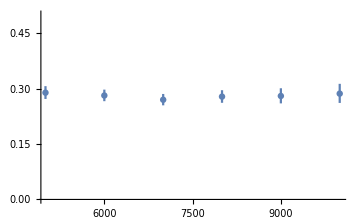
{-Graphics-,-Graphics-}

{754,906,915,765,539,349}

```mathematica
data = data3Windowed;

{atomWindowStart,atomWindowEnd, atomWindowWidth, atomWindowStep} =Round[{2.5,13,5,1}10^3];
atomWindows = Table[{x,x+atomWindowWidth}, {x, atomWindowStart, atomWindowEnd-atomWindowWidth, atomWindowStep}];

correlsHoms=HomCorrelationsWindowed[data,{{det1,det1},{det1,det2},{det2,det2}}, #]&/@atomWindows;

(*nbars ={(Length@#[[2]])/Total[Length/@#],(√(Length@#[[2]]))/Total[Length/@#]}&/@correlsHoms;*)
nbars ={(Length@#[[2]])/Total[Length/@#],CorrectedWilsonScore[Total[Length/@#],Length@#[[2]],0.688]-(Length@#[[2]])/Total[Length/@#]}&/@correlsHoms;

(*correlsHoms=HomCorrelationsWindowedBkgCorr[data,{{det1,det1},{det1,det2},{det2,det2}}, #]&/@atomWindows;
nbars ={(#[[2]])/Total[#],CorrectedWilsonScore[Total[#],#[[2]],0.688]-(#[[2]])/Total[#]}&/@correlsHoms;*)

{ErrorListPlot[MakeNice[Mean/@atomWindows,nbars[[;;,1]],nbars[[;;,2]]],PlotRange->{0,0.5},ImageSize->Medium],
LabelledMOTHistogram[data,{atomWindowStart,atomWindowEnd},{0,0.1}]
}
Length@Flatten@#&/@correlsHoms
```

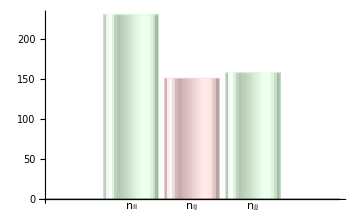
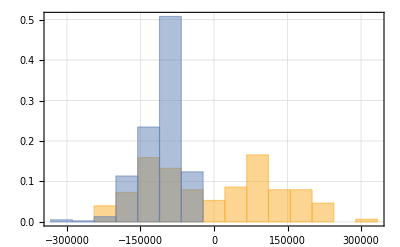

```mathematica
i=5;
nbins=15;
{
BarChart[Length/@correlsHoms[[i]],ChartLabels->{"n_ii","n_ij","n_jj"},ChartStyle->{LightGreen, LightRed, LightGreen},ChartElementFunction->"GlassRectangle",ImageSize->Medium],
homHist = Histogram[{correlsHoms[[i,2]],Join[correlsHoms[[i,1]],correlsHoms[[i,3]]]},{-photonLength,photonLength,2photonLength/nbins}/2,"Probability",genOpts]
}
```

#### n̄ and HOM as function of throw number

```mathematica
{det1,det2}=detectors;
```

```mathematica
FilterAndHomCorrelations[data_, detPairs_]:=Module[{data2Limited, data3Windowed},
data2Limited=Select[data,Between[Length[#],coarseCountCutOffs]&];
data2Limited=CompensateDetectorLags[data2Limited,Transpose[{Sort[detectors],lag[#]&/@Sort[detectors]}],photonLength];
data2Limited=FilterByStirapRange[data2Limited,stirapLimits];
data2Limited=Select[data2Limited,Between[Length[#],fineCountCutOffs]&];

data3Windowed=FilterByPulseRange[data2Limited,atomWindow];

HomCorrelations[data3Windowed,detPairs]
]
```

```mathematica
Needs["ErrorBarPlots`"]
MakeNice[x_,y_,σy_]:=Sort@Transpose[{Transpose[{x,y}],ErrorBar/@σy}]
```

{-Graphics-,-Graphics-}

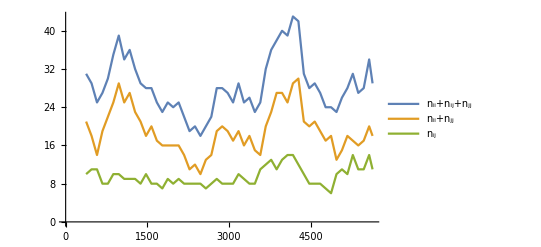

{31,29,25,27,30,35,39,34,36,32,29,28,28,25,23,25,24,25,22,19,20,18,20,22,28,28,27,25,29,25,26,23,25,32,36,38,40,39,43,42,31,28,29,27,24,24,23,26,28,31,27,28,34,29}

```mathematica
data = data1Raw;

{throwWindowStart,throwWindowEnd, throwWindowWidth, thowWindowStep} =Round[{1,Length@data,750,100}];
throwWindows = Table[{If[x==0,1,x],If[x+throwWindowWidth>Length@data,Length@data,x+throwWindowWidth]}, {x, throwWindowStart, throwWindowEnd-(throwWindowWidth-thowWindowStep), thowWindowStep}];

correlsHoms=FilterAndHomCorrelations[data[[ #[[1]];;#[[2]] ]],{{det1,det1},{det1,det2},{det2,det2}}]&/@throwWindows;


(*nbars ={(Length@#[[2]])/Total[Length/@#],(√(Length@#[[2]]))/Total[Length/@#]}&/@correlsHoms;*)nbars ={(Length@#[[2]])/Total[Length/@#],CorrectedWilsonScore[Total[Length/@#],Length@#[[2]],0.688]-(Length@#[[2]])/Total[Length/@#]}&/@correlsHoms;

addRunMarkersProlog = With[{totLen=Total[dataFileLengths]},Line[{Scaled[{#/totLen,0}],Scaled[{#/totLen,1}]}]&/@(Accumulate[dataFileLengths])];

{ErrorListPlot[MakeNice[Mean/@throwWindows,nbars[[;;,1]],nbars[[;;,2]]],
PlotRange->{{0,Length@data},{0,0.5}},
ImageSize->Medium,
Prolog->addRunMarkersProlog
],

ListLinePlot[Transpose[{Mean/@throwWindows,nbars[[;;,1]]}],
PlotRange->{{0,Length@data},{0,0.5}},
ImageSize->Medium,
Prolog->addRunMarkersProlog
]
}

ListLinePlot[
{Transpose[{Mean/@throwWindows,Length@Flatten@#&/@correlsHoms}],
Transpose[{Mean/@throwWindows,Length@Flatten@#&/@correlsHoms[[;;,{1,3}]]}],
Transpose[{Mean/@throwWindows,Length@Flatten@#&/@correlsHoms[[;;,2]]}]},
PlotLegends->{"n_ii+n_ij+n_jj","n_ii+n_jj","n_ij"}]
Length@Flatten@#&/@correlsHoms
```

```mathematica
p=2;
slideStep = 10000;
slideWindow = 60000;
slidingCorrelationTest = Table[rCorrWindowed=Length[ Select[#[[p]], Function[corr,start<Abs@corr<slideWindow+start]] ]/If[Length@#[[p]]==0,1,Length[#[[p]]]]&/@correlsHoms;

minimisation = N/@Minimize[Mean@Abs[x*rCorrWindowed - Rescale@nbars[[;;,1]]],x];
{minimisation[[1]],minimisation[[2,1,2]]},

{start,0,330000-slideWindow,slideStep}];

indexBestCorr=(Position[#,Min[#]]&@slidingCorrelationTest[[;;,1]])[[1,1]];
{R,bestCorrWindowStart}={slidingCorrelationTest[[indexBestCorr,2]],slideWindow/2+Range[0,300000-slideWindow,slideStep][[indexBestCorr]]}
```

Thread::tdlen: Objects of unequal length in {{{{1,{{1,548067,3413880834,5141},{2,491479,3494176968,5262},{1,518438,4413944384,6647},{1,532362,4609195547,6941},{1,528638,5010955920,7546},{1,133171,5496661647,8278},{1,488484,5844326574,8801},{1,439506,5857558875,8821},{1,409148,6520937219,9820},{2,446711,6675703704,10053},{1,424529,6677673750,10056}}},{2,{{1,624489,1676743412,2525},{2,119004,3331106578,5017},{2,185711,5259639992,7921},{2,613722,5383585347,8107},{2,138110,8253231249,12429},{2,382514,11731223396,17666}}},«48»,«951»},{4/13,{-0.142574,0.178614}}},«49»,«47»} {0,1/11,1/11,1/8,1/8,«42»,2/11,1/5,1/7,«4»} cannot be combined.

$Aborted

{3.70901,170000}

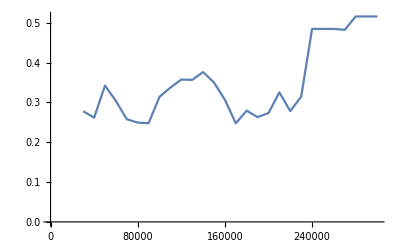

```mathematica
ListLinePlot[Transpose[{ slideWindow/2+Range[0 ,330000-slideWindow,slideStep],slidingCorrelationTest[[;;,1]]} ]]
```

```mathematica
p=2;
rCorrWindowed=Length[ Select[#[[p]], Function[corr,bestCorrWindowStart<Abs@corr<bestCorrWindowStart+slideWindow]] ]/If[Length@#[[p]]==0,1,Length[#[[p]]]]&/@correlsHoms;

(*minimisation = N/@Minimize[Mean@Abs[x*rCorrWindowed - Rescale@nbars[[;;,1]]],x]
R=minimisation[[2,1,2]];*)

ListLinePlot[{
Transpose[{Mean/@throwWindows,R*rCorrWindowed}],
Transpose[{Mean/@throwWindows,Rescale@nbars[[;;,1]]}]
(*Transpose[{Mean/@throwWindows,Abs[R*rCorrWindowed - Rescale@nbars[[;;,1]]]}]*)
},
PlotRange->{{0,Length@data},{0,1}},
PlotStyle->{Automatic,Automatic,Dashed},
ImageSize->Large,
AspectRatio->1/2,
Prolog->addRunMarkersProlog]
```

-Graphics-

Try fitting different decoherence lengths over the course of the day

```mathematica
p=2;
slideStep = 5000;
slideWindow = 30000;

maxOverlapsOdSlidingCorrelationTestOnSubruns=
Table[
	Module[{slidingCorrelationTest},
slidingCorrelationTest = Table[
Length[ Select[#[[p]], Function[corr,start<Abs@corr<slideWindow+start]] ]/If[Length@#[[p]]==0,1,Length[#[[p]]]]&@correlsHoms[[i]],
{start,0,330000-slideWindow,slideStep}
];
{(slideWindow/2+Range[0 ,330000-slideWindow,slideStep])[[Position[slidingCorrelationTest,Max@slidingCorrelationTest][[1,1]]]],Max@slidingCorrelationTest}
],
{i,1,Length@correlsHoms}
];
```

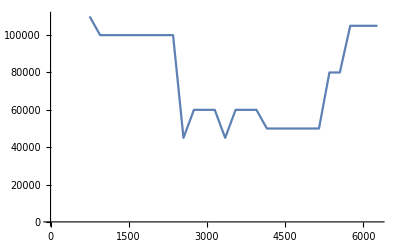

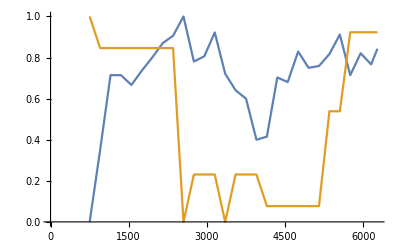

```mathematica
ListLinePlot[
{
Transpose[{Mean/@throwWindows,maxOverlapsOdSlidingCorrelationTestOnSubruns[[;;,1]]}]
}
]
ListLinePlot[
{
Transpose[{Mean/@throwWindows,Rescale@nbars[[;;,1]]}],
Transpose[{Mean/@throwWindows,Rescale[#,MinMax@#,{0,1}]&@maxOverlapsOdSlidingCorrelationTestOnSubruns[[;;,1]]}]
}
]
```

#### Post-select data by nbar value

```mathematica
Filter[data_]:=Module[{data2Limited, data3Windowed},
data2Limited=Select[data,Between[Length[#],coarseCountCutOffs]&];
data2Limited=CompensateDetectorLags[data2Limited,Transpose[{Sort[detectors],lag[#]&/@Sort[detectors]}],photonLength];
data2Limited=FilterByStirapRange[data2Limited,stirapLimits];
data2Limited=Select[data2Limited,Between[Length[#],fineCountCutOffs]&];

data3Windowed=FilterByPulseRange[data2Limited,atomWindow]
]
```

```mathematica
data = data1Raw;
dataIndexed = Transpose[{Range[1,Length@data,1],data}];

{throwWindowStart,throwWindowEnd, throwWindowWidth, thowWindowStep} =Round[{1,Length@data,1000,100}];
throwWindows = Table[{If[x==0,1,x],If[x+throwWindowWidth>Length@data,Length@data,x+throwWindowWidth]}, {x, throwWindowStart, throwWindowEnd-(throwWindowWidth-thowWindowStep), thowWindowStep}];

correlsHoms=FilterAndHomCorrelations[data[[ #[[1]];;#[[2]] ]],{{det1,det1},{det1,det2},{det2,det2}}]&/@throwWindows;

(*nbars ={(Length@#[[2]])/Total[Length/@#],(√(Length@#[[2]]))/Total[Length/@#]}&/@correlsHoms;*)
nbars ={(Length@#[[2]])/Total[Length/@#],CorrectedWilsonScore[Total[Length/@#],Length@#[[2]],0.688]-(Length@#[[2]])/Total[Length/@#]}&/@correlsHoms;
```

```mathematica
nbarMax = 0.25;
nbarMin = 0.36;

x=Transpose[{dataIndexed[[ #[[1]];;#[[2]] ]]&/@throwWindows, nbars}];

highVisData=Select[x,#[[2,1]]<nbarMax&][[;;,1]];
highVisDataLimited = DeleteDuplicatesBy[Flatten[highVisData,1], #[[1]]&];
highVisDataLimited=Filter[highVisDataLimited[[;;,2]]];

lowVisData=Select[x,#[[2,1]]>nbarMin&][[;;,1]];
lowVisDataLimited = DeleteDuplicatesBy[Flatten[lowVisData,1], #[[1]]&];
lowVisDataLimited=Filter[lowVisDataLimited[[;;,2]]];
```

```mathematica
Length@data1Raw
Length/@{Flatten[highVisData,1],Flatten[lowVisData,1]}
Length/@{highVisDataLimited,lowVisDataLimited}
```

10556

{17017,30030}

{4792,5985}

#### Odd/Even g^(2)'s

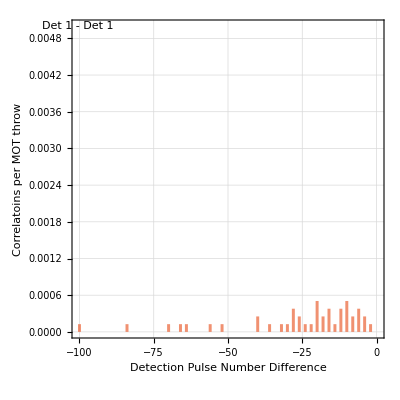
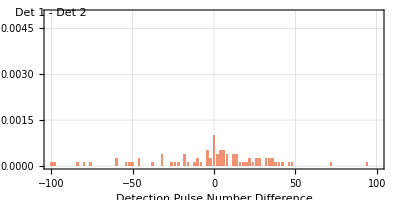
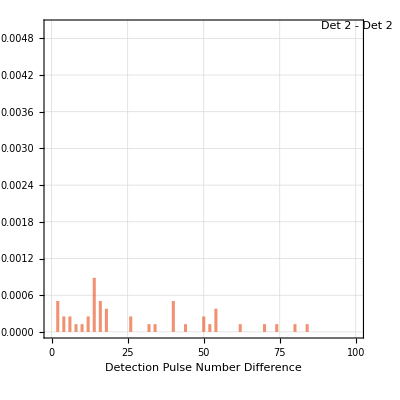
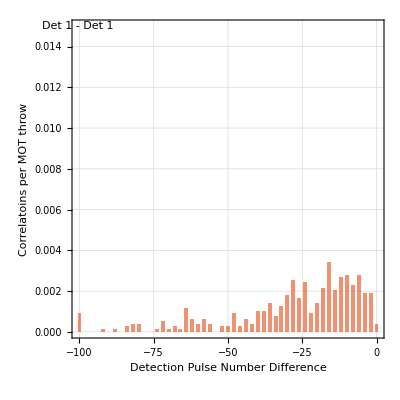
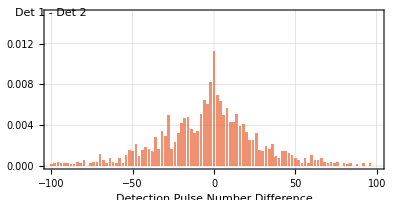
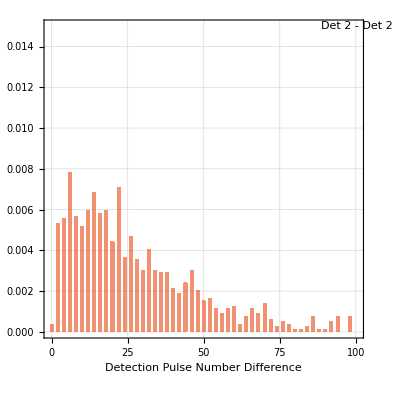

```mathematica
LabelledG2Histogram[#,detectors[[1]],detectors[[2]]]&/@FilterByPulseParities[data3Windowed,{EvenQ,OddQ}]
```

### Conditional Histograms

```mathematica
StirapSubHistogram2[data_,nbins_,col_,opts:OptionsPattern[]]:=Module[{dataAtom,nAtom,σAtom,N1,N2,bc,amp,limitedPhotonLength},

limitedPhotonLength=-Subtract@@stirapLimits;

dataAtom=Flatten[data[[;;,;;,2]]];

nAtom=Length[dataAtom];

σAtom=√nAtom;

N1=N@Length[data];
N2=limitedPhotonLength/nbins 10^-6;

{nAtom,σAtom}={nAtom,σAtom}/N1;

bc=BinCounts[dataAtom,{0.,limitedPhotonLength,limitedPhotonLength/nbins}]/(N1 N2);
amp=Max[bc];

ListStepPlot[bc,"Center",DataRange->{0.,limitedPhotonLength/1000.},
PlotStyle->Directive[AbsoluteThickness[0.8],Black],
Filling->{1->{Axis,col}},
Epilog->{
Text[UncertaintyForm[{nAtom,σAtom},1],Scaled[{0.98,0.98}],Scaled[{1,1}],Background->Directive[Opacity[1],White]]
},
opts
]
]
```

```mathematica
DetectionGrid4[data_,detectors_,userMax_:0]:=Module[{subdividedDataGrid,nbins,max,hopts,cols,frameLabels},

subdividedDataGrid=FilterByDetector[#,detectors]&/@FilterByPulseParities[data,{EvenQ,OddQ}];

nbins=20;
If[userMax==0,
max=Max[HistogramList[Flatten[#[[;;,;;,2]]],{0,photonLength,photonLength/20}][[2]]&/@Join@@subdividedDataGrid],
max=userMax
];
hopts=Sequence[Frame->True,GridLines->Automatic,PlotRangePadding->None,PlotRange->{{0,photonLength/1000.},{0,5Ceiling[max/5.]/($NTHROWS photonLength/nbins 10^-6)}},ImageSize->150,AspectRatio->0.8];

cols=Map[ColorData[97],{{4,Sequence@@ConstantArray[1,Length[detectors]-1],3},{4,Sequence@@ConstantArray[1,Length[detectors]-1],3},{2,Sequence@@ConstantArray[2,Length[detectors]-1],5}},{2}];

frameLabels={{
{{"Evens",None},{None,"Detector "<>ToString[detectors[[1]]]}},
Sequence@@({{"",None},{None,"Detector "<>ToString[#]}}&/@detectors[[2;;]])
},{
{{"Odds",None},{None,""}},
Sequence@@ConstantArray[{{"",None},{None,""}},{6}]
}};

Grid@MapIndexed[
StirapSubHistogram2[#1,nbins,cols[[Sequence@@#2]],FrameLabel->frameLabels[[Sequence@@#2]],hopts]&,
subdividedDataGrid,
{2}
]
]
```

```mathematica
data=data3Windowed;

t=1;
flatRiffledData=Join@@Riffle[DeleteCases[data,{}],{{{-1,-1,-1,-1}}}];
ditheredDiffs=(Prepend[#,1]*Append[#,1])&@(Differences[flatRiffledData[[;;,4]]]-t);
homBunches=Split[Pick[flatRiffledData,ditheredDiffs,0],Last[#1]==Last[#2]-1&];
homPairs=Flatten[Partition[#,2,1]&/@homBunches,1];
```

```mathematica
grid=Function[{m},Pick[m,m[[;;,1,1]],#]&/@detectors]/@(Pick[homPairs,#@homPairs[[;;,1,4]],True]&/@{EvenQ,OddQ});
```

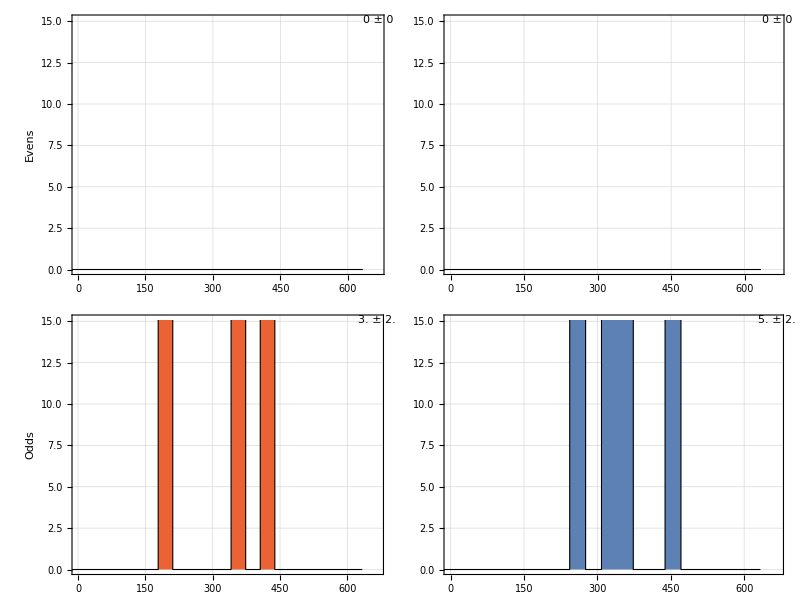
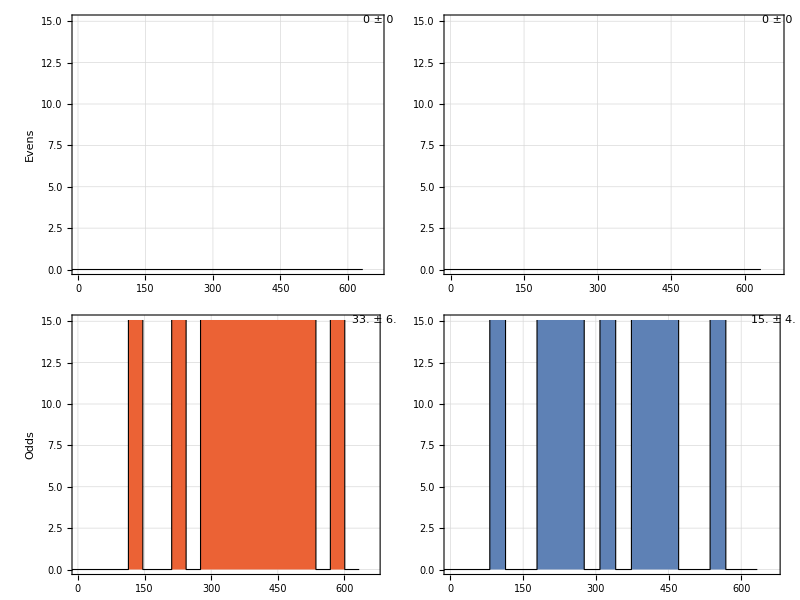
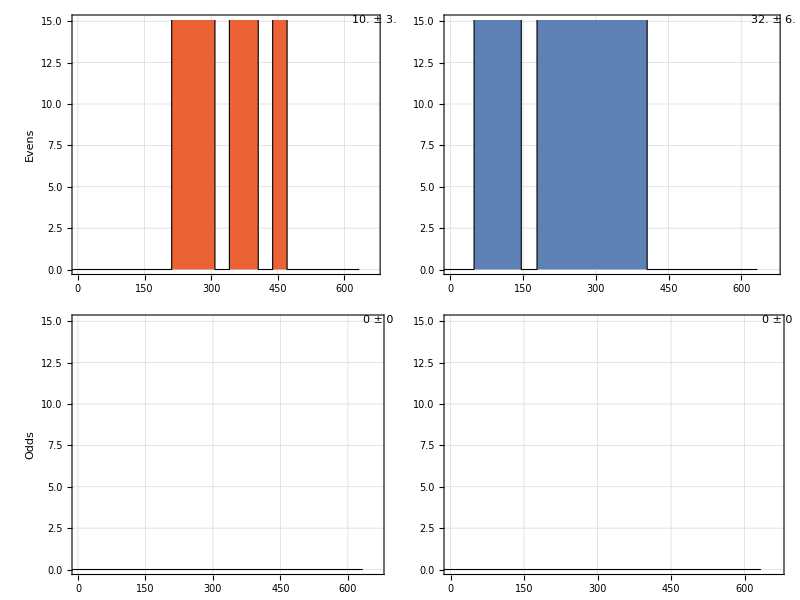
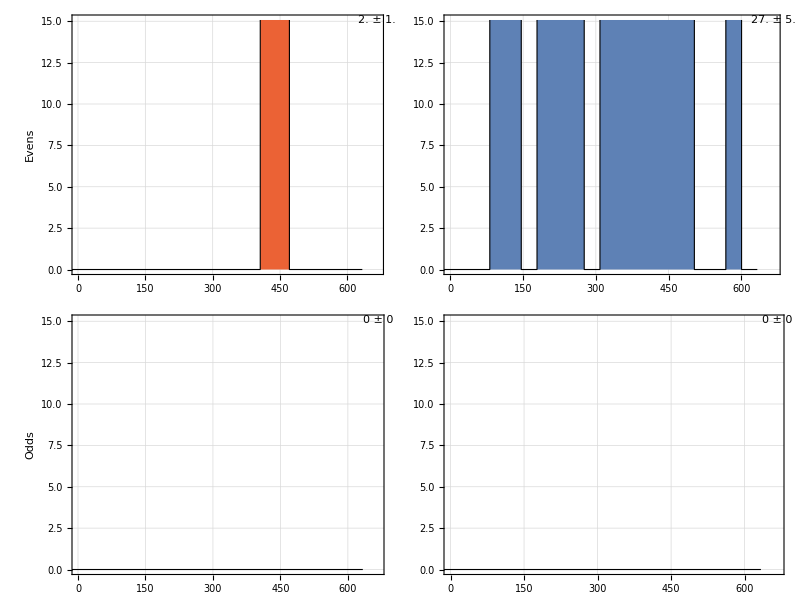
| Detector 0 | Detector 1
Evens | -Graphics- | -Graphics-
Odds | -Graphics- | -Graphics-

```mathematica
m4=Map[DetectionGrid4[{#},detectors,1000]&,grid[[;;,;;,;;,2]],{2}];
a=0.8;
Grid[ArrayFlatten[{{{{Null}},{{"Detector 0","Detector 1"}}},{{{Rotate["Evens",π/2]},{Rotate["Odds",π/2]}},m4}}],
Background->{None,None,{
{1,1}->GrayLevel[0.9],
{1,2}->GrayLevel[0.9],
{1,3}->GrayLevel[0.9],
{2,1}->GrayLevel[0.9],
{3,1}->GrayLevel[0.9],
{2,2}->Lighter[ColorData[97][4],a],
{3,3}->Lighter[ColorData[97][4],a],
{2,3}->Lighter[ColorData[97][1],a],
{3,2}->Lighter[ColorData[97][1],a]
}},
Frame->True
]
```

### Detection Patterns

```mathematica
keys={{0},{1},{2},{0,0},{0,2},{2,0},{1,1},{2,2},{0,2,0},{2,0,2},{0,0,0}};
m=Max[keys]+1;
lens=Union[Length/@keys];


diffs=Developer`ToPackedArray/@(Differences/@data3Windowed[[;;,;;,4]]);
as=Join@@ParallelTable[
Counts[Pick[#,UnitStep[(Max/@#)-m],0]&@(Join@@(Partition[#,l,1]&/@diffs))],
{l,lens}
];

TableForm[{keys,as/@keys},TableDepth->2,TableAlignments->Center]
```

{0} | {1} | {2} | {0,0} | {0,2} | {2,0} | {1,1} | {2,2} | {0,2,0} | {2,0,2} | {0,0,0}
42 | 127 | 104 | Missing[KeyAbsent,{0,0}] | 2 | Missing[KeyAbsent,{2,0}] | 2 | 5 | Missing[KeyAbsent,{0,2,0}] | Missing[KeyAbsent,{2,0,2}] | Missing[KeyAbsent,{0,0,0}]

```mathematica
correlsHom=HomCorrelations[data3Windowed,{{0,0},{0,2},{2,2}}];
Length[Flatten[correlsHom]]
```

14

### G2 Table 16

```mathematica
N[Length[HomCorrelations[data3Windowed,{{0,1}}][[1]]]/Length[data3Windowed]]
UncertaintyPlus[#[[1,2]],#[[2,1]]]&@NCorrelationsPerThrow[data3Windowed,{0,1},{2}]
```

0.

{0.,0.}

```mathematica
Clear[Data16]
Data16[data_,det1_,det2_,hideIdx_List,constrainRange_:{0,50}]:=Module[{dataDet1,dataDet2,idx0,correls,key,fEven,fOdd,fBoth,fEmpties,g2DataEvenOddBothEmpty,dataEvenOddBothEmpty},

(*Remove MOT throws where no detections on a detector*)
{dataDet1,dataDet2}=FilterByDetector[data,{det1,det2}];
idx0=Union[Flatten[Position[Length/@#,0]&/@{dataDet1,dataDet2},1]];
{dataDet1,dataDet2}=Delete[#,idx0]&/@{dataDet1,dataDet2};

(*Generate key based on correlations - expand*)
correls=Outer[Plus,#[[1,;;,4]],-#[[2,;;,4]]]&/@Transpose[{dataDet1,dataDet2}];
key=Clip[Abs[correls],constrainRange,{-1,-1}];
key=Abs[correls]/.x_:>-1/;Or[MemberQ[hideIdx,x],x>constrainRange[[2]]];

fEven=Function[{list},With[{plist=Select[list,NonNegative]},If[plist==={},False,And@@(EvenQ/@plist)]]];
fOdd=Function[{list},With[{plist=Select[list,NonNegative]},If[plist==={},False,And@@(OddQ/@plist)]]];
fBoth=Function[{list},With[{plist=Select[list,NonNegative]},If[plist==={},False,ContainsAll[(EvenQ/@plist),{True,False}]]]];
fEmpties=Function[{list},And@@(Negative/@list)];

g2DataEvenOddBothEmpty=
Map[Function[{f},Join@@@Transpose[{Pick[dataDet1,(f/@#)&/@key,True],Pick[dataDet2,(f/@Transpose[#])&/@key,True]}]],{fEven,fOdd,fBoth,fEmpties}];

dataEvenOddBothEmpty=Map[FilterByDetector[#,{det1,det2}]&,g2DataEvenOddBothEmpty];

(*4x4 array of standard data objects, filtered by Even Odd Both Empty*)
Outer[
(SortBy[#,#[[3]]&]&/@(Join@@@Transpose[{#1,#2}]))&,
dataEvenOddBothEmpty[[;;,1]],
dataEvenOddBothEmpty[[;;,2]],
1
]
]
```

```mathematica
data16=Data16[data3Windowed,0,4,{0},{0,10}];
```

```mathematica
TableForm[data16/.{Rule[ImageSize,_]:>Rule[ImageSize,400],Rule[PlotRange,{xr_,yr_}]:>Rule[PlotRange,{xr,{0,0.1}}]},TableHeadings->{{"Even","Odd","Both","Empty"},{"Even","Odd","Both","Empty"}},TableAlignments->Center];
```

### Other / Additional

```mathematica
NCorrelationsPerThrow[data3Windowed,{0,2},{1}]
```

{{{0.,0.},{0.,0.}},{{0.,0.},{0.0205631,0.0033764}}}

```mathematica
TableForm[
NCorrelationsPerThrow[data3Windowed,{0,2},{1}][[;;,;;,1]]
]
TableForm[
NCorrelationsPerThrow[data3Windowed,{0,2},{1}][[;;,;;,2]]
]
TableForm[
(#/Total[#,2])&@NCorrelationsPerThrow[data3Windowed,{0,2},{1}][[;;,;;,1]]
]
```

0. | 0.
0. | 0.0205631

0. | 0.
0. | 0.0033764

0. | 0.
0. | 1.

```mathematica
{{0.011653225806451614, 0.}, {0., 0.}}
```

{{0.0116532,0.},{0.,0.}}

```mathematica
PM1CorrelationsPerThrow[data3Windowed,detectors[[1]],detectors[[2]]]
```

{0.079814,0.00654078}

```mathematica
{0.08938609842719432,0.007922240806302916}
```

{0.0893861,0.00792224}

Ignoring Background effects

```mathematica
nEven=Total[Function[{m},Count[m[[;;,4]],x_/;EvenQ[x]]]/@data3Windowed];
nOdd=Total[Function[{m},Count[m[[;;,4]],x_/;OddQ[x]]]/@data3Windowed];

nOddAfterEven=Total[Function[{m},SequenceCount[m[[;;,4]],{x_,y_}/;EvenQ[x]&&y==x+1]]/@data3Windowed];
nEvenAfterOdd=Total[Function[{m},SequenceCount[m[[;;,4]],{x_,y_}/;OddQ[x]&&y==x+1]]/@data3Windowed];

ηOddAfterEven=N@nOddAfterEven/nEven;
ηEvenAfterOdd=N@nEvenAfterOdd/nOdd;

{nEven,nOdd}
{nEvenAfterOdd,nOddAfterEven}
{ηEvenAfterOdd,ηOddAfterEven}
ηRatio=ηOddAfterEven/ηEvenAfterOdd
```

{3938,4236}

{71,56}

{0.0167611,0.0142204}

0.848418

```mathematica
nEven=Total[Function[{m},Count[m[[;;,{1,4}]],{d_,x_}/;EvenQ[x]&&d==0]]/@data3Windowed]
nOdd=Total[Function[{m},Count[m[[;;,{1,4}]],{d_,x_}/;OddQ[x]&&d==2]]/@data3Windowed]

nOddAfterEven=Total[Function[{m},SequenceCount[m[[;;,{1,4}]],{{dx_,x_},{dy_,y_}}/;EvenQ[x]&&y==x+1&&dx==0&&dy==2]]/@data3Windowed]
nEvenAfterOdd=Total[Function[{m},SequenceCount[m[[;;,{1,4}]],{{dx_,x_},{dy_,y_}}/;OddQ[x]&&y==x+1&&dx==2&&dy==0]]/@data3Windowed]

ηOddAfterEven=N@nOddAfterEven/nEven
ηEvenAfterOdd=N@nEvenAfterOdd/nOdd

ηRatio=ηOddAfterEven/ηEvenAfterOdd
```

0

1965

0

0

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

0.

Power::infy: Infinite expression 1/0. encountered.

Indeterminate

```mathematica
nEven=Total[Function[{m},Count[m[[;;,4]],x_/;EvenQ[x]]]/@#]&/@FilterByDetector[data3Windowed,{0,1}]
nOdd=Total[Function[{m},Count[m[[;;,4]],x_/;OddQ[x]]]/@#]&/@FilterByDetector[data3Windowed,{0,1}]

nOddAfterEven=Total[Function[{m},SequenceCount[m[[;;,4]],{x_,y_}/;EvenQ[x]&&y==x+1]]/@#]&/@FilterByDetector[data3Windowed,{0,1}]
nEvenAfterOdd=Total[Function[{m},SequenceCount[m[[;;,4]],{x_,y_}/;OddQ[x]&&y==x+1]]/@#]&/@FilterByDetector[data3Windowed,{0,1}]

ηOddAfterEven=N@nOddAfterEven/nEven
ηEvenAfterOdd=N@nEvenAfterOdd/nOdd

ηRatio=ηOddAfterEven/ηEvenAfterOdd
```

{0,747}

{0,2271}

{0,4}

{0,11}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,0.00535475}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,0.00484368}

{Indeterminate,1.10551}

### Tom

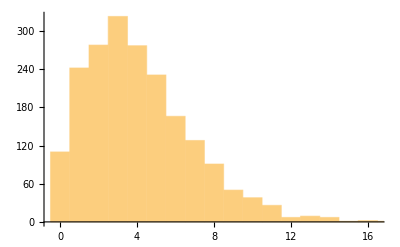

```mathematica
Histogram[Length/@data3Windowed,{1},"Count"]
```